```mathematica
hepData=Import["/Users/samiyrjanheikki/Downloads/HEPData-ins617784-v1-csv/Table1.csv"];
pT=hepData[[All,1]];
σ=hepData[[All,4]];
pythia=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/pT_histogram.csv"];
pT2=pythia[[All,1]];
σ2=pythia[[All,2]];
pythia5e6=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/pT_histogram_5e6.csv"];
pT5e6=pythia5e6[[All,1]];
σ5e6=pythia5e6[[All,2]];
pythia5e64=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/pT_histogram_5e6_4.csv"];
pT5e64=pythia5e64[[All,1]];
σ5e64=pythia5e64[[All,2]];
```

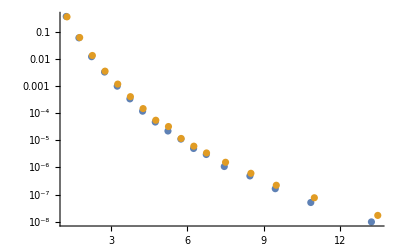

```mathematica
plot=Show[ListLogPlot[Transpose[{pT,σ}]],ListLogPlot[Transpose[{pT2,σ2}],PlotStyle->ColorData[97,"ColorList"][[2]]],PlotRange->All]
```

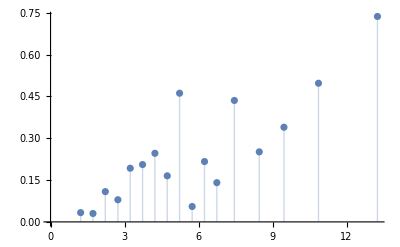

```mathematica
errors=ListPlot[Transpose[{pT,Abs[σ-σ2]/σ}],Filling->Axis]
```

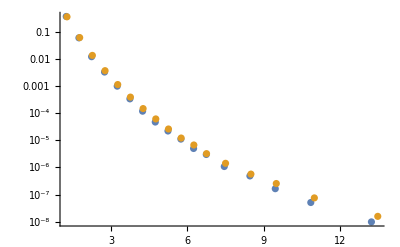

```mathematica
plot2=Show[ListLogPlot[Transpose[{pT,σ}]],ListLogPlot[Transpose[{pT5e6,σ5e6}],PlotStyle->ColorData[97,"ColorList"][[2]]],PlotRange->All]
```

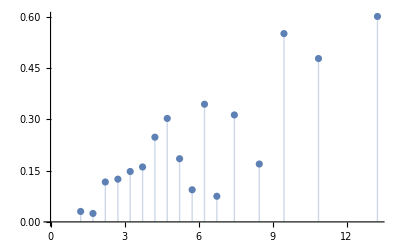

```mathematica
errors5e6=ListPlot[Transpose[{pT,Abs[σ-σ5e6]/σ}],Filling->Axis]
```

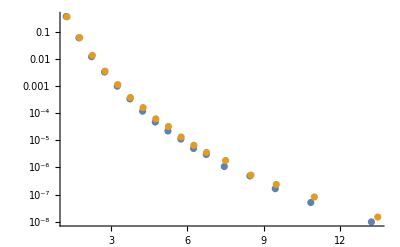

```mathematica
plot3=Show[ListLogPlot[Transpose[{pT,σ}]],ListLogPlot[Transpose[{pT5e64,σ5e64}],PlotStyle->ColorData[97,"ColorList"][[2]]],PlotRange->All]
```

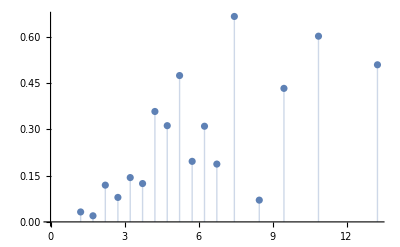

```mathematica
errors5e64=ListPlot[Transpose[{pT,Abs[σ-σ5e64]/σ}],Filling->Axis]
```

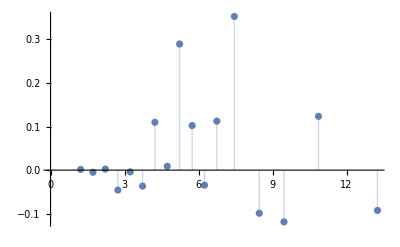

```mathematica
errorDeltas=ListPlot[Transpose[{pT,Abs[σ-σ5e64]/σ-Abs[σ-σ5e6]/σ}],Filling->Axis]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/sigma5e6.pdf",plot2]
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/errors.pdf",errors5e6]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/sigma5e6.pdf

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/errors.pdf

```mathematica
pythia6=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/pT_histogram_6.csv"];
pT6=pythia[[All,1]];
σ6=pythia[[All,2]];
```

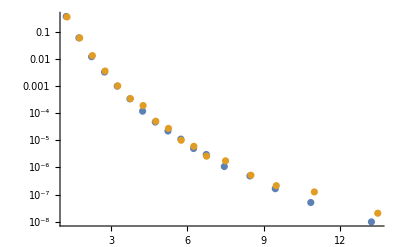

```mathematica
Show[ListLogPlot[Transpose[{pT,σ}]],ListLogPlot[Transpose[{pT6,σ6}],PlotStyle->ColorData[97,"ColorList"][[2]]],PlotRange->All]
```

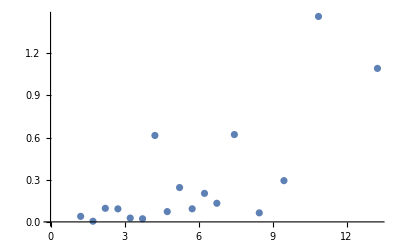

```mathematica
ListPlot[Transpose[{pT,Abs[σ-σ6]/σ}]]
```